Práctica 1: Curvas en el plano y en el espacio.
Nombre y apellidos: Mario Román García

Primer parte: Curvas planas.

Objetivo: Utilizar Mathematica para definir y dibujar curvas planas, calcular diedros de Frenet y curvaturas, y obtener curvas con curvatura prefijada.

Definición de curvas: Veamos cómo se define en Mathematica una curva parametrizada α(t) con parámetro t.

Ejemplos:

```mathematica
alpha1[t_]:={t^3,t^2};
```

```mathematica
alpha2[t_]:={Cos[t],Sin[4t]};
```

Comandos para la representación gráfica de curvas:
Plot
Plot[f[x], {x, a, b}] dibuja el grafo de la función f(x) en el intervalo [a,b]. Observa el efecto de los diferentes comandos:

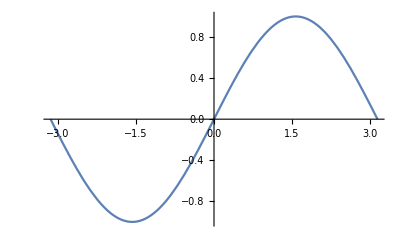

```mathematica
Plot[Sin[t],{t,-Pi,Pi}]
```

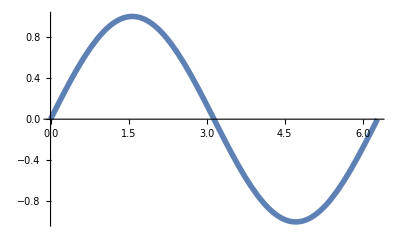

```mathematica
Plot[Sin[t],{t,0,2Pi},PlotStyle->{Thickness[0.01]}]
```

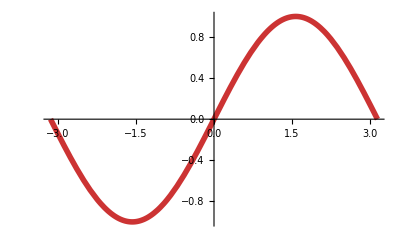

```mathematica
Plot[Sin[t],{t,-Pi,Pi},PlotStyle->{{Thickness[0.01],RGBColor[0.8,0.2,0.2]}}]
```

```mathematica
graf1=Plot[Sin[t],{t,0,2Pi},PlotStyle->{{Thickness[0.01],RGBColor[0.8,0.2,0.2],Dashing[{0.06}]}}]
```

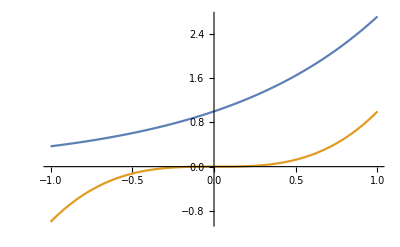

```mathematica
graf2=Plot[{E^t,t^3},{t,-1,1}]
```

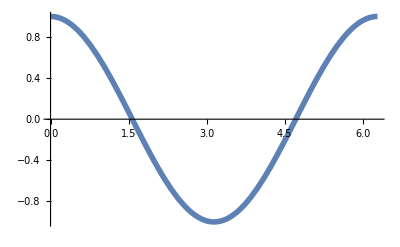

```mathematica
graf3=Plot[Cos[t],{t,0,2Pi},PlotStyle->{Thickness[0.01]}]
```

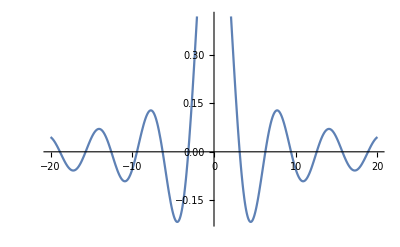

```mathematica
Plot[Sin[t]/t,{t,-20,20}]
```

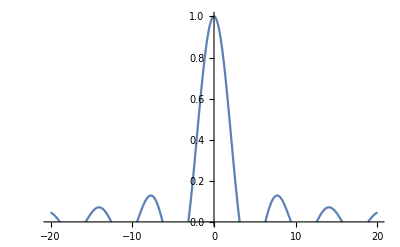

```mathematica
Plot[Sin[t]/t,{t,-20,20},PlotRange->{0,1}]
```

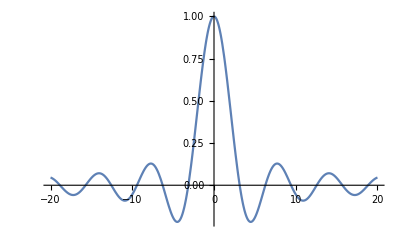

```mathematica
Plot[Sin[t]/t,{t,-20,20},PlotRange->All]
```

Show
Show[graphics, options] muestra uno o varios gráficos usando las opciones especificadas.

```mathematica
Show[graf1,graf3]
```

Show::gcomb: Could not combine the graphics objects in Show[graf1,].

Show[graf1,-Graphics-]

ParametricPlot
ParametricPlot[{x[t], y[t]}, {t, a, b}] dibuja la curva plana α(t)=(x(t),y(t)) en el intervalo [a,b].

```mathematica
ParametricPlot[alpha1[t]//Evaluate,{t,-3,3}]
```

```mathematica
ParametricPlot[alpha2[t]//Evaluate,{t,0,2Pi}]
```

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]
```

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}, AspectRatio->Automatic]
```

Ejemplos de curvas planas famosas:

El folium de Descartes.

```mathematica
folium[t_]:={3t/(1+t^3),3t^2/(1+t^3)};
```

```mathematica
ParametricPlot[folium[t]//Evaluate,{t,-1,5},AspectRatio->Automatic,Ticks->None,PlotPoints->55]
```

Espiral logarítmica de parámetros a y b.

```mathematica
logspiral[a_,b_][t_]:=E^(a t) {Cos[b t],Sin[b t]};
```

```mathematica
ParametricPlot[logspiral[1,10][t]//Evaluate,{t,0,Pi},AspectRatio->Automatic,Ticks->None,PlotPoints->55]
```

Cicloide de parámetros a y b.

```mathematica
cycloid[a_,b_][t_]:={b Sin[t]-a t,a-b Cos[t]}
```

```mathematica
ParametricPlot[cycloid[1,1][t]//Evaluate,{t,-Pi/2,5Pi/2},AspectRatio->Automatic]
```

Lemniscata de Bernouilli de parámetro a. Observa cómo se emplea la orden Table para dibujar varias lemniscatas con diferente parámetro.

```mathematica
lemniscate[a_][t_]:={a Cos[t]/(1+Sin[t]^2),a Sin[t] Cos[t]/(1+Sin[t]^2)}
```

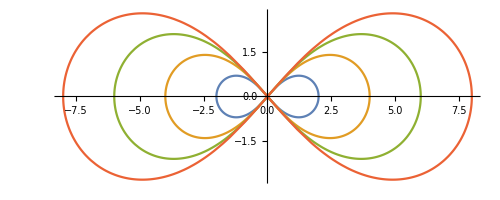

```mathematica
ParametricPlot[Table[lemniscate[a][t],{a,2,8,2}]//Evaluate,{t,0,2Pi},AspectRatio->Automatic]
```

Cardioide de parámetro a. Observa cómo se emplea la orden Table para dibujar varias cardioides con diferente parámetro.

```mathematica
cardioid[a_][t_]:={2a Cos[t] (1+Cos[t]),2a Sin[t] (1+Cos[t])}
```

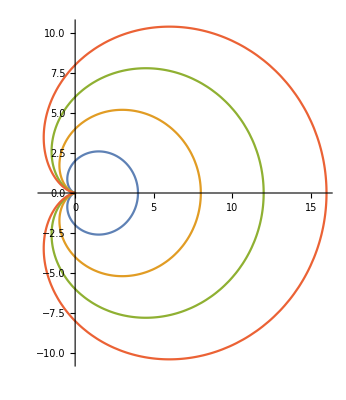

```mathematica
ParametricPlot[Table[cardioid[a][t],{a,1,4,1}]//Evaluate,{t,0,2Pi},AspectRatio->Automatic]
```

Cisoide de Diocles de parámetro a.

```mathematica
cissoid[a_][t_]:={2a t^2/(1+t^2),2a t^3/(1+t^2)}
```

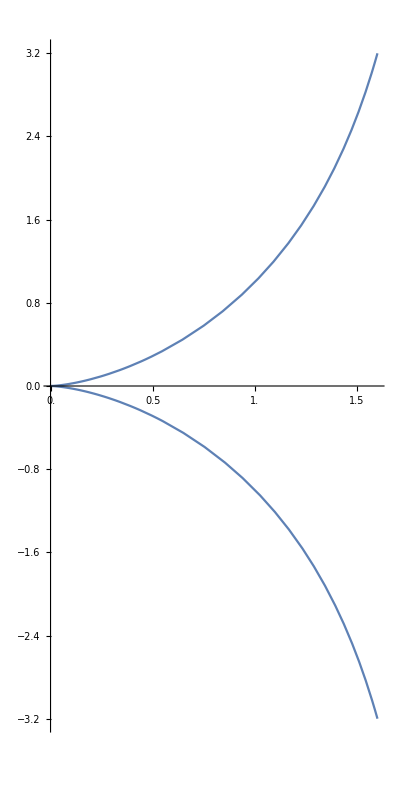

```mathematica
ParametricPlot[cissoid[1][t]//Evaluate,{t,-2,2},AspectRatio->2,Ticks->{Range[0,2,0.5],Automatic},PlotRange->All]
```

Tractriz de parámetro a.

```mathematica
tractrix[a_][t_]:=a{Sin[t],Cos[t]+Log[Tan[t/2]]}
```

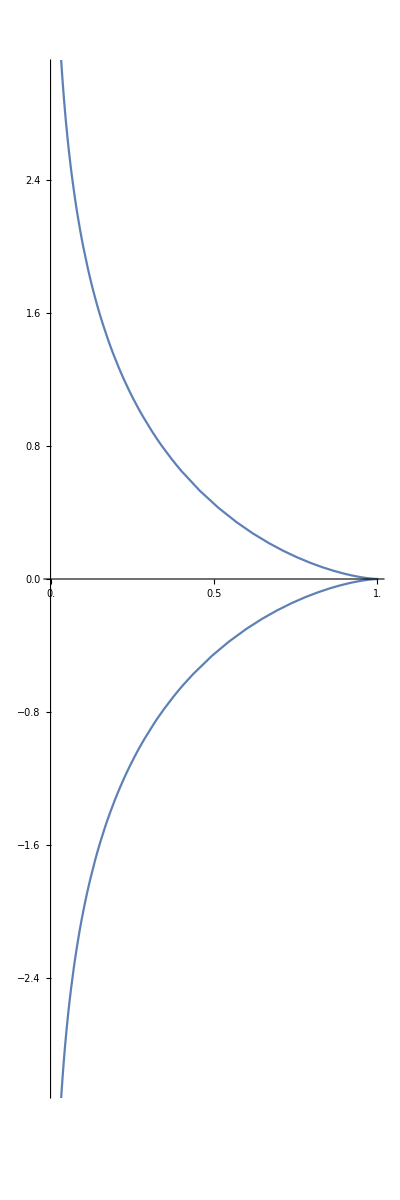

```mathematica
ParametricPlot[tractrix[1][t]//Evaluate,{t,0.01,0.99 Pi},AspectRatio->3,PlotPoints->50,PlotRange->{Automatic,{-3.0,3.0}},Ticks->{Range[0,1,0.5],Automatic}]
```

Ejercicios:

1. Dibuja tres “curvas lágrima” (teardrop curves) (puedes encontrar su parametrización en el enlace web número 2 al final de la práctica) practicando los comandos de dibujo anteriores.  
2. Busca en los apuntes de clase un ejemplo de curva continua con longitud infinita en un intervalo compacto. Define y representa gráficamente dicha curva.

```mathematica
teardrop[m_][t_] := {Cos[t], Sin[t] * Sin[1/2* t]^m}
```

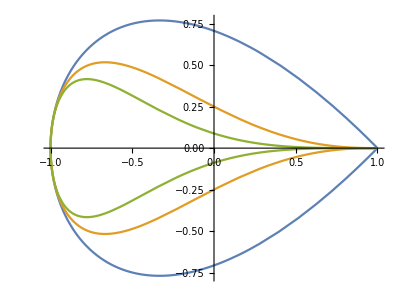

```mathematica
ParametricPlot[Table[teardrop[m][t],{m,1,7,3}]//Evaluate,{t,0,2Pi},AspectRatio->Automatic]
```

```mathematica
ejemploclase[t_] := {t,t*Cos[Pi/t]}
ejemploclasetrozos[t_] := Piecewise[{{0 ,t==0}},ejemploclase[t]]
```

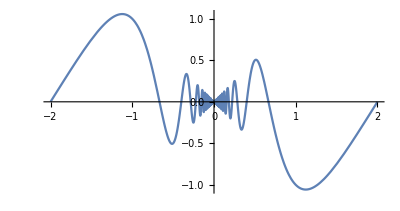

```mathematica
ParametricPlot[ejemploclasetrozos[t]//Evaluate,{t,-2,2},AspectRatio->Automatic]
```

Diedro de Frenet y curvatura de una curva plana:

Vector tangente de una curva regular plana.

```mathematica
tangent[alpha_][t_]:=D[alpha[u],u]/Simplify[Factor[D[alpha[u],u].D[alpha[u],u]]]^(1/2) /. u->t
```

```mathematica
tangent[alpha1][t]
```

{(3 t^2)/(√(t^2 (4+9 t^2))),(2 t)/(√(t^2 (4+9 t^2)))}

```mathematica
tangent[alpha1][t]//Simplify//PowerExpand
```

{(3 t)/(√(4+9 t^2)),2/(√(4+9 t^2))}

```mathematica
tangent[alpha2][t]
```

{-Sin[t]/(√(16 Cos[4 t]^2+Sin[t]^2)),(4 Cos[4 t])/(√(16 Cos[4 t]^2+Sin[t]^2))}

Vector normal de una curva regular plana.

```mathematica
J:={{0,-1},{1,0}}
```

```mathematica
normal[alpha_][t_]:=J.tangent[alpha][t]
```

```mathematica
normal[alpha1][t]
```

{-(2 t)/(√(t^2 (4+9 t^2))),(3 t^2)/(√(t^2 (4+9 t^2)))}

```mathematica
normal[alpha1][t]//Simplify//PowerExpand
```

{-2/(√(4+9 t^2)),(3 t)/(√(4+9 t^2))}

```mathematica
normal[alpha2][t]//FullSimplify
```

{-(4 Cos[4 t])/(√(8+8 Cos[8 t]+Sin[t]^2)),-Sin[t]/(√(8+8 Cos[8 t]+Sin[t]^2))}

Curvatura de una curva regular plana:

```mathematica
kappa[alpha_][t_]:=Det[{D[alpha[u],u],D[alpha[u],{u,2}]}]/
Simplify[D[alpha[u],u].D[alpha[u],u]]^(3/2)/.u->t
```

```mathematica
kappa[alpha1][t]//Simplify //PowerExpand
```

-6/(t (4+9 t^2)^(3/2))

```mathematica
kappa[alpha2][t]//Simplify
```

(2 (5 Cos[3 t]-3 Cos[5 t]))/((16 Cos[4 t]^2+Sin[t]^2)^(3/2))

```mathematica
kappa[logspiral[a,b]][t]//Simplify
```

Det::matsq: Argument {logspiral[a,b]'[u],logspiral[a,b]''[u]} at position 1 is not a non-empty square matrix.

Det::matsq: Argument {logspiral[a,b]'[t],logspiral[a,b]''[t]} at position 1 is not a non-empty square matrix.

Det[{logspiral[a,b]'[t],logspiral[a,b]''[t]}]/(logspiral[a,b]'[t].logspiral[a,b]'[t])^(3/2)

Ejercicios:

3. Recuerda cómo se define la evoluta de una curva plana (ejercicio 11 de la relación 1). Sea α(t)=(sen(2t) cos(t), sen(2t) sen(t)) y sea β(t) la evoluta de α(t). Representa
sobre un mismo gráfico y con colores distintos las trazas de ambas curvas. Calcula también sus diedros de Frenet y sus curvaturas.

```mathematica
alpha[t_] := {Sin[2*t]*Cos[t], Sin[2*t]*Sin[t]}
```

```mathematica
evoluta[alpha_][t_] := alpha[t] + (1/kappa[alpha][t])*normal[alpha][t]
```

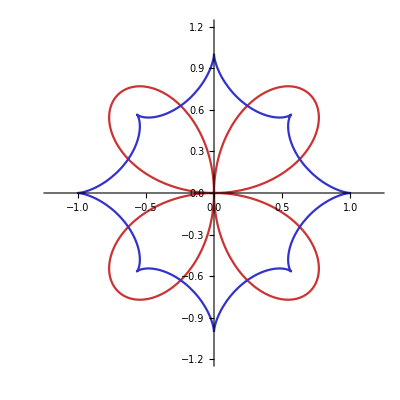

```mathematica
Show[
  ParametricPlot[alpha[t]//Evaluate,{t,-Pi,Pi},AspectRatio->Automatic,PlotRange->{{-1.2,1.2},{-1.2,1.2}},PlotStyle->{{RGBColor[0.8,0.2,0.2]}}],
  ParametricPlot[evoluta[alpha][t]//Evaluate,{t,-Pi,Pi},AspectRatio->Automatic,PlotRange->{{-1.2,1.2},{-1.2,1.2}},PlotStyle->{{RGBColor[0.2,0.2,0.8]}}]
]
```

```mathematica
tangent[alpha][t] // FullSimplify
normal[alpha][t] // FullSimplify
kappa[alpha][t] // FullSimplify
```

{(Cos[t]+3 Cos[3 t])/(√(10+6 Cos[4 t])),(-Sin[t]+3 Sin[3 t])/(√(10+6 Cos[4 t]))}

{(Sin[t]-3 Sin[3 t])/(√(10+6 Cos[4 t])),(Cos[t]+3 Cos[3 t])/(√(10+6 Cos[4 t]))}

(√2 (13+3 Cos[4 t]))/(5+3 Cos[4 t])^(3/2)

```mathematica
tangent[evoluta[alpha]][t] // FullSimplify
normal[evoluta[alpha]][t] // FullSimplify
kappa[evoluta[alpha]][t] // FullSimplify
```

{(√2 (488 Cos[t]+314 Cos[3 t]+198 Cos[5 t]+15 Cos[7 t]+9 Cos[9 t]) Sin[t]^2)/((13+3 Cos[4 t])^2 √(((5+3 Cos[4 t]) (58 Sin[4 t]+3 Sin[8 t])^2)/(13+3 Cos[4 t])^4)),(√2 Cos[t]^2 (-488 Sin[t]+314 Sin[3 t]-198 Sin[5 t]+15 Sin[7 t]-9 Sin[9 t]))/((13+3 Cos[4 t])^2 √(((5+3 Cos[4 t]) (58 Sin[4 t]+3 Sin[8 t])^2)/(13+3 Cos[4 t])^4))}

{(√2 Cos[t]^2 (488 Sin[t]-314 Sin[3 t]+198 Sin[5 t]-15 Sin[7 t]+9 Sin[9 t]))/((13+3 Cos[4 t])^2 √(((5+3 Cos[4 t]) (58 Sin[4 t]+3 Sin[8 t])^2)/(13+3 Cos[4 t])^4)),(√2 (488 Cos[t]+314 Cos[3 t]+198 Cos[5 t]+15 Cos[7 t]+9 Cos[9 t]) Sin[t]^2)/((13+3 Cos[4 t])^2 √(((5+3 Cos[4 t]) (58 Sin[4 t]+3 Sin[8 t])^2)/(13+3 Cos[4 t])^4))}

(√2 (13+3 Cos[4 t]))/(3 (5+3 Cos[4 t]) √(((5+3 Cos[4 t]) (58 Sin[4 t]+3 Sin[8 t])^2)/(13+3 Cos[4 t])^4))

Determinación de una curva plana a partir de su curvatura

Recuerda el enunciado del teorema fundamental para curvas planas. Su demostración se puede implementar en Mathematica para dibujar curvas planas con curvatura prefijada. Para ello utilizaremos comandos de resolución numérica de ecuaciones diferenciales. Veamos un ejemplo:

Curva con curvatura k(s) = s:

```mathematica
k[s_]:=s
```

```mathematica
theta[s_]:=Integrate[k[u],{u,0,s}]
```

```mathematica
curva[s_]:=NDSolve[{x'[s]==Cos[theta[s]],y'[s]==Sin[theta[s]],x[0]==0,y[0]==0},{x,y},{s,-10,10}];
```

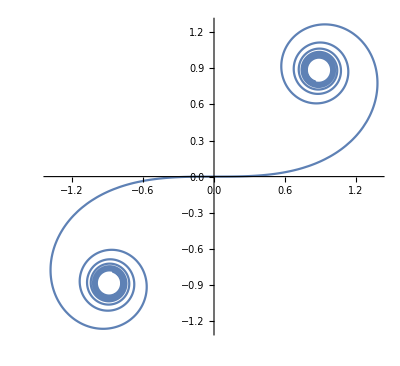

```mathematica
ParametricPlot[Evaluate[{x[s],y[s]}/.curva[s]],{s,-10,10},AspectRatio->Automatic]
```

Ejercicios:

4. Representa las curvas planas que tienen por curvaturas las funciones k(s) = -7, k(s) = s cos(s) y k(s) = s^2+s+1.

```mathematica
curvaConCurvatura[k_] := NDSolve[{x'[s] == Cos[Integrate[k[u],{u,0,s}]], y'[s] == Sin[Integrate[k[u],{u,0,s}]],x[0]==0,y[0]==0},{x,y},{s,-10,10}]
```

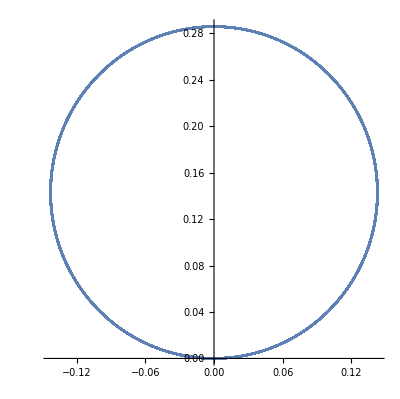

```mathematica
k1[t_] := 7; 
ParametricPlot[Evaluate[{x[s],y[s]}/.curvaConCurvatura[k1]],{s,-10,10},AspectRatio -> Automatic]
```

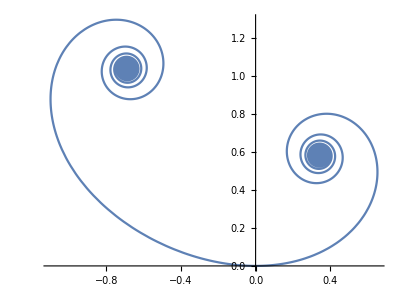

```mathematica
k2[t_] := t^2 + t + 1; 
ParametricPlot[Evaluate[{x[s],y[s]}/.curvaConCurvatura[k2]],{s,-10,10},AspectRatio -> Automatic]
```

Segunda parte: Curvas en el espacio.

Objetivo: Utilizar Mathematica para dibujar curvas en el espacio, calcular triedros de Frenet, curvaturas y torsiones, y para obtener curvas con curvatura y torsión prefijadas.

Definición de curvas: Veamos cómo se define una curva parametrizada de parámetro t en el espacio.

Ejemplos:

```mathematica
gamma[t_]:={3 t-t^3,3 t^2,3 t+t^3};
```

```mathematica
elipse[t_]:={0,2 Cos[t],5 Sin[t]};
```

```mathematica
logespiralhelix[t_]:={E^(0.08 t)  Cos[t],E^(0.08 t)  Sin[t],t};
```

Representación gráfica de curvas parametrizadas en el espacio:

ParametricPlot3D
ParametricPlot3D[{x[t], y[t], z[t]}, {t, a, b}] dibuja la curva (x(t), y(t), z(t)) en el intervalo [a,b].

```mathematica
ParametricPlot3D[gamma[t]//Evaluate,{t,-2,2}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[elipse[t]//Evaluate,{t,0,2^Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[logespiralhelix[t]//Evaluate,{t,0,10Pi},AspectRatio->Automatic,Ticks->None,PlotPoints->50]
```

-Graphics3D-

Show
Show[lista de gráficos, opciones] muestra uno o varios gráficos, usando las opciones especificadas.

```mathematica
graf4=ParametricPlot3D[{Cos[t],Sin[t],(1/2)t},{t,-2Pi,2Pi}, AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
graf5=ParametricPlot3D[{Cos[t],0,Sin[2t]},{t,0,2 Pi}, AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
Show[graf4,graf5,Boxed->False,Axes->False,ViewPoint->{1,0.5,1}]
```

-Graphics3D-

Algunos ejemplos de curvas en el espacio famosas:

Hélices circulares de eje vertical.

```mathematica
helice[a_,b_][t_]:={a Cos[t],a Sin[t],b t};
```

```mathematica
ParametricPlot3D[helice[1,0.2][t]//Evaluate,{t,0,6 Pi},PlotPoints->200,PlotRange->{{-1,1},{-1,1},{0, Pi}}]
```

-Graphics3D-

Hélices generalizadas sobre curvas planas.

```mathematica
helical[alpha_,c_][t_]:={alpha[t][[1]],alpha[t][[2]],c t};
```

```mathematica
alpha[t_]:={Cos[t],Sin[2t]};
```

```mathematica
ParametricPlot3D[helical[alpha,1/2][t]//Evaluate,{t,-2Pi,2Pi},PlotPoints->200]
```

-Graphics3D-

Curvas de Viviani.

```mathematica
viviani[a_][t_]:=a{1+Cos[t],Sin[t],2Sin[t/2]};
```

```mathematica
ParametricPlot3D[{viviani[1][t],viviani[3][t]}//Evaluate,{t,0,2Pi}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{viviani[1][t],viviani[3][t]}//Evaluate,{t,0,2Pi},Boxed->False,
ViewPoint->{10,3,1},Axes->False]
```

-Graphics3D-

Ejercicios:

5. Representa sobre un mismo gráfico una familia formada por 3 hélices circulares con el mismo parámetro b y distinto parámetro a.
6. Define y representa gráficamente sobre un mismo gráfico tres astroides tridimensionales (la parametrización general de un astroide es α(t)=(a (cos(t))^n, b (sen(t))^n, cos(2t)).

```mathematica
ParametricPlot3D[{helice[1,0.2][t],helice[0.2,0.2][t],helice[0.6,0.2][t]}//Evaluate,{t,0,6 Pi},Boxed->False,Axes->False,PlotRange->{{-1,1},{-1,1},{0, Pi}}]
```

-Graphics3D-

```mathematica
astroide[n_,a_,b_][t_]:={a(Cos[t]^n), b(Sin[t]^n),Cos[2*t]}
```

```mathematica
ParametricPlot3D[{astroide[1,1,1][t],astroide[3,1.5,1.5][t],astroide[5,2,2][t]}//Evaluate,{t,0,2 Pi},PlotPoints->100,Boxed->False,PlotRange->{{-2,2},{-2,2},{-2, 2}}]
```

-Graphics3D-

Triedro de Frenet, curvatura y torsión de una curva en el espacio:

Vector tangente unitario de una curva regular.

```mathematica
tangente[alpha_][t_]:=D[alpha[u],u]/Sqrt[D[alpha[u],u].D[alpha[u],u]] /. u->t
```

```mathematica
tangente[gamma][t]
```

{(3-3 t^2)/(√(36 t^2+(3-3 t^2)^2+(3+3 t^2)^2)),(6 t)/(√(36 t^2+(3-3 t^2)^2+(3+3 t^2)^2)),(3+3 t^2)/(√(36 t^2+(3-3 t^2)^2+(3+3 t^2)^2))}

```mathematica
tangente[gamma][t]//Simplify//PowerExpand
```

{-(-1+t^2)/(√2 (1+t^2)),(√2 t)/(1+t^2),1/(√2)}

```mathematica
tangente[elipse][t]//Simplify
```

{0,-(2 Sin[t])/(√(25 Cos[t]^2+4 Sin[t]^2)),(5 Cos[t])/(√(25 Cos[t]^2+4 Sin[t]^2))}

Vector binormal de una curva regular (en los puntos en los que tenga sentido).

```mathematica
binormal[alpha_][t_]:=Cross[D[alpha[u],u],D[alpha[u],{u,2}]]/Sqrt[Cross[D[alpha[u],u],D[alpha[u],{u,2}]].Cross[D[alpha[u],u],D[alpha[u],{u,2}]]] /. u->t
```

```mathematica
binormal[gamma][t]
```

{(-18+18 t^2)/(√(1296 t^2+(-18+18 t^2)^2+(18+18 t^2)^2)),-(36 t)/(√(1296 t^2+(-18+18 t^2)^2+(18+18 t^2)^2)),(18+18 t^2)/(√(1296 t^2+(-18+18 t^2)^2+(18+18 t^2)^2))}

```mathematica
binormal[gamma][t]//Simplify//PowerExpand
```

{(-1+t^2)/(√2 (1+t^2)),-(√2 t)/(1+t^2),1/(√2)}

```mathematica
binormal[elipse][t]//FullSimplify
```

{1,0,0}

Vector normal de una curva regular (en los puntos en los que tenga sentido).

```mathematica
normal[alpha_][t_]:=Cross[binormal[alpha][t],tangente[alpha][t]] /. u->t
```

```mathematica
normal[gamma][t]
```

{-(2 t)/(1+t^2),-(-1+t^2)/(1+t^2),0}

```mathematica
normal[gamma][t]//Simplify//PowerExpand
```

{-(2 t)/(1+t^2),(1-t^2)/(1+t^2),0}

```mathematica
normal[elipse][t]//FullSimplify
```

{0,-(5 √2 Cos[t])/(√(29+21 Cos[2 t])),-(2 √2 Sin[t])/(√(29+21 Cos[2 t]))}

Curvatura de una curva regular en el espacio.

```mathematica
curvatura[alpha_][t_]:=Sqrt[Cross[D[alpha[u],u],D[alpha[u],{u,2}]].Cross[D[alpha[u],u],D[alpha[u],{u,2}]]]/
(D[alpha[u],u].D[alpha[u],u])^(3/2) /. u->t
```

```mathematica
curvatura[gamma][t]//Simplify //PowerExpand
```

1/(3 (1+t^2)^2)

```mathematica
curvatura[elipse][t]//FullSimplify
```

10/((25 Cos[t]^2+4 Sin[t]^2)^(3/2))

Torsión de una curva regular en el espacio (en los puntos donde la curvatura es positiva).

```mathematica
modulo[v] := Sqrt[v.v];
torsion[alpha_][t_]:=-Det[{D[alpha[u],u], D[alpha[u],{u,2}],D[alpha[u],{u,3}]}]
  /(modulo[Cross[D[alpha[u],u],D[alpha[u],{u,2}]]]^2) /. u -> t
```

```mathematica
torsion[gamma][t]//Simplify //PowerExpand
```

-216

```mathematica
torsion[elipse][t]//Simplify
```

0

Ejercicios:

7. Elige una de las curvas del ejercicio 6 y calcula su triedro de Frenet, su curvatura y su torsión. Representa en un mismo gráfico la traza de la curva junto con su recta afín binormal en el instante t = 0.

```mathematica
elegida := helical[alpha,1/2]
tangente[elegida][t] //FullSimplify
normal[elegida][t] //FullSimplify
binormal[elegida][t] //FullSimplify
curvatura[elegida][t] //FullSimplify
torsion[elegida][t] //FullSimplify
```

{-(2 Sin[t])/(√(11-2 Cos[2 t]+8 Cos[4 t])),(4 Cos[2 t])/(√(11-2 Cos[2 t]+8 Cos[4 t])),1/(√(11-2 Cos[2 t]+8 Cos[4 t]))}

{(-9 Cos[t]+4 (-3 Cos[3 t]+Cos[5 t]))/(√(Cos[t]^2 (105-96 Cos[2 t]+8 Cos[4 t])) √(11-2 Cos[2 t]+8 Cos[4 t])),(2 (-6 Sin[2 t]+Sin[4 t]))/(√(Cos[t]^2 (105-96 Cos[2 t]+8 Cos[4 t])) √(11-2 Cos[2 t]+8 Cos[4 t])),(-Sin[2 t]+8 Sin[4 t])/(√(Cos[t]^2 (105-96 Cos[2 t]+8 Cos[4 t])) √(11-2 Cos[2 t]+8 Cos[4 t]))}

{(4 Sin[2 t])/(√(Cos[t]^2 (105-96 Cos[2 t]+8 Cos[4 t]))),-Cos[t]/(√(Cos[t]^2 (105-96 Cos[2 t]+8 Cos[4 t]))),(6 Cos[t]-2 Cos[3 t])/(√(Cos[t]^2 (105-96 Cos[2 t]+8 Cos[4 t])))}

(4 √(Cos[t]^2 (105-96 Cos[2 t]+8 Cos[4 t])))/(11-2 Cos[2 t]+8 Cos[4 t])^(3/2)

-4 Cos[u]^3

```mathematica
rectaafinbinormalencero[t] := elegida[0] + t*binormal[elegida][0];
ParametricPlot3D[{elegida[t],rectaafinbinormalencero[t]}//Evaluate,{t,-2Pi,2Pi},PlotPoints->200]
```

-Graphics3D-

Determinación de una curva en el espacio a partir de su curvatura y su torsión:

Recuerda el enunciado del teorema fundamental para curvas en el espacio. La demostración está basada en la existencia y unicidad de solución de un sistema de ecuaciones diferenciales ordinarias de primer orden. Dicho sistema puede resolverse con Mathematica para dibujar curvas en el espacio que tengan curvatura y torsión prefijadas. Para ello utilizaremos comandos de resolución numérica de ecuaciones diferenciales. Veamos un ejemplo:

Curva con curvatura k(s) = 5 y torsión t(s) = -1 (obviamente debe obtenerse una hélice circular):

```mathematica
k[s_]:=5;t[s_]:=-1
```

```mathematica
curva=NDSolve[{x'[s]==t1[s],y'[s]==t2[s],z'[s]==t3[s],
t1'[s]==k[s]n1[s],t2'[s]==k[s]n2[s],t3'[s]==k[s]n3[s],
n1'[s]==-k[s]t1[s]-t[s]b1[s],n2'[s]==-k[s]t2[s]-t[s] b2[s],
n3'[s]==-k[s] t3[s]-t[s] b3[s],
b1'[s]==t[s] n1[s],b2'[s]==t[s] n2[s],b3'[s]==t[s] n3[s],
x[0]==0,y[0]==0,z[0]==0,
t1[0]==1,t2[0]==0,t3[0]==0,
n1[0]==0,n2[0]==1,n3[0]==0,
b1[0]==0,b2[0]==0,b3[0]==1},
{x,y,z,t1,t2,t3,n1,n2,n3,b1,b2,b3},
{s,-10,10}];
```

```mathematica
ParametricPlot3D[Evaluate[{x[s],y[s],z[s]}/.curva],{s,-10,10},ViewPoint->{1,1,1},
AspectRatio->Automatic,PlotPoints->100]
```

-Graphics3D-

Ejercicio:

8. Determina y representa las curvas en el espacio que tienen las siguientes curvaturas y torsiones:
	(a).   k(s) = s-1; t(s) = 0.8
	(b).   k(s) = s; t(s) = cos(s)
	(c).   k(s) =  sen(s); t(s) = cos(s)

```mathematica
curvaConCurvaturaYTorsion[k_,t_] := NDSolve[{x'[s]==t1[s],y'[s]==t2[s],z'[s]==t3[s],
t1'[s]==k[s]n1[s],t2'[s]==k[s]n2[s],t3'[s]==k[s]n3[s],
n1'[s]==-k[s]t1[s]-t[s]b1[s],n2'[s]==-k[s]t2[s]-t[s] b2[s],
n3'[s]==-k[s] t3[s]-t[s] b3[s],
b1'[s]==t[s] n1[s],b2'[s]==t[s] n2[s],b3'[s]==t[s] n3[s],
x[0]==0,y[0]==0,z[0]==0,
t1[0]==1,t2[0]==0,t3[0]==0,
n1[0]==0,n2[0]==1,n3[0]==0,
b1[0]==0,b2[0]==0,b3[0]==1},
{x,y,z,t1,t2,t3,n1,n2,n3,b1,b2,b3},
{s,-10,10}];
```

```mathematica
ka[s_] := s-1 
ta[s_] := 0.8
kb[s_] :=s
tb[s_] :=Cos[s]
kc[s_] :=Sin[s]
tc[s_] :=Cos[s]
```

```mathematica
Evaluate[{x[2],y[2],z[2]}/.curvaConCurvaturaYTorsion[ka,ta]]
```

{{1.84116,-0.711412,0.0400925}}

```mathematica
ParametricPlot3D[
Evaluate[{x[s],y[s],z[s]}/.curvaConCurvaturaYTorsion[ka,ta]]
,{s,-10,10}]
ParametricPlot3D[
Evaluate[{x[s],y[s],z[s]}/.curvaConCurvaturaYTorsion[kb,tb]]
,{s,-10,10}]
ParametricPlot3D[
Evaluate[{x[s],y[s],z[s]}/.curvaConCurvaturaYTorsion[kc,tc]]
,{s,-10,10}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

Algunos enlaces en internet sobre curvas:

1. Índice de curvas famosas:  	www-gap.dcs.st-and.ac.uk/~history/Curves/Curves.html

2. World of Mathematics. Curvas planas:  http://mathworld.wolfram.com/topics/GeneralPlaneCurves.html

3. Curvas chulas en el plano:    http://www.xahlee.org/SpecialPlaneCurves_dir/specialPlaneCurves.html

Instrucciones al terminar la práctica:

1. Graba la práctica y no olvides escribir tu nombre en el espacio que hay reservado para ello al comienzo.
2. Asegúrate de que has realizado todos los ejercicios y de que todas las celdas se evaluan sin problemas.
3. Borra las celdas de salida: busca el comando Delete All Output en alguna de las pestañas del menú superior (Cell o Notebook). Graba.